```mathematica
(* Seeing if can determine B^x along x-dir to one higher order than lowest order *)
(* Sasha would determine dBdx's polynomial coefficients for left and right cells centered on cell center, where point-valued dBx/dx is known from differencing a2c_i B^i across cell center *)
(* Here x/dx=0 is cell center, x/dx=1/2 is right cell face of interest and x/dx=-1/2 is the left cell face of interest *)
dBdxraw[x_]:=F0+F1/dx (x/dx-0) + F2 /dx(x/dx-0)^2+ F3 /dx(x/dx-0)^3+ F4 /dx(x/dx-0)^4+ F5 /dx(x/dx-0)^5+ F6 /dx(x/dx-0)^6;
```

```mathematica
(* The dBdxraw has constraints, but let place them later through the use of the a2c_i function *)
```

```mathematica
(* Now form integral that is distribution of Bx in the left and right cell with Bxl0 and Bxr0 cell center point values of field *)
Bx[t_]:=Bx0+Integrate[Evaluate[dBdxraw[x]],{x,0*dx,t}]
```

```mathematica
(* Now setup equation that determines Bx0, that is a2c_i B^i = known quantity *)
(* We want to form a2c_i B^i, which requires forming another function f=a2c_i Bx such that c2a_i f=Bx *)
f[x_]:=f0+f1/dx (x/dx-0) + f2 /dx(x/dx-0)^2+ f3 /dx(x/dx-0)^3+ f4 /dx(x/dx-0)^4+ f5 /dx(x/dx-0)^5+ f6 /dx(x/dx-0)^6+ f7 /dx(x/dx-0)^7;
RunningAverage[t_]:=FullSimplify[Integrate[f[x],{x,t-dx/2,t+dx/2}]/dx];
```

```mathematica
(* Now obtain coefficients of f from those of Bx *)
```

```mathematica
sol=Solve[CoefficientList[RunningAverage[x],x] ==CoefficientList[Bx[x],x],{f0,f1,f2,f3,f4,f5,f6,f7}]
```

{{f0→(40320 Bx0-1680 F1+294 F3-155 F5)/40320,f1→(6720 dx^2 F0-560 dx F2+196 dx F4-155 dx F6)/6720,f2→1/96 (48 dx F1-12 dx F3+7 dx F5),f3→1/48 (16 dx F2-8 dx F4+7 dx F6),f4→1/24 (6 dx F3-5 dx F5),f5→1/20 (4 dx F4-5 dx F6),f6→(dx F5)/6,f7→(dx F6)/7}}

```mathematica
a2cBx[x_]:=f[x]//.sol[[1]]
```

```mathematica
(* now have a2c_i B^i distribution that has to give back known a2c_i B^i's, use this to obtain Bxl0 and Bxr0 assuming rest will correctly give back correct distribution of B^i *)
```

```mathematica
fun1=FullSimplify[a2cBx[1/2*dx]]
fun2=FullSimplify[a2cBx[-1/2*dx]]
sol12=FullSimplify[Solve[{fun1==a2cright,fun2==a2cleft},{Bx0,F0}]]
FullSimplify[(fun1-fun2)/dx//.sol12[[1]]]
```

Bx0+(dx F0)/2+F1/12-F3/120+F5/252

Bx0-(dx F0)/2+F1/12-F3/120+F5/252

{{Bx0→1/120 (60 a2cleft+60 a2cright-10 F1+F3)-F5/252,F0→(-a2cleft+a2cright)/dx}}

(-a2cleft+a2cright)/dx

```mathematica
(* Get final Bxl and Bxr distributions *)
```

```mathematica
myBx[x_]:=FullSimplify[Bx[x]//.sol[[1]]]//.sol12[[1]]
```

0.65+0.3 x

-0.5 (-2.04462+x) (0.513543+x (0.544621+x))

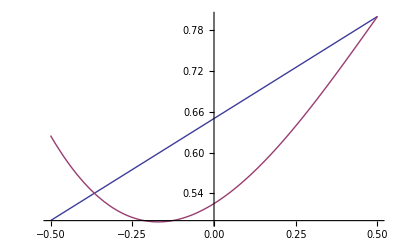

```mathematica
toplotBxlinear=FullSimplify[myBx[x]//.{dx->1,a2cleft->.5,a2cright->.8,F1->0,F2->0,F3->0,F4->0,F5->0,F6->0}]
toplotBxnonlinear=FullSimplify[myBx[x]//.{dx->1,a2cleft->.5,a2cright->.8,F1->1.5,F2->-F1,F3->0,F4->0,F5->0,F6->0}]
Plot[{toplotBxlinear,toplotBxnonlinear},{x,-1/2,1/2}]
```

```mathematica
(* Get final a2c_i B^i distributions *)
mya2cBx[x_]:=FullSimplify[a2cBx[x]//.sol[[1]]]//.sol12[[1]]
```

```mathematica
(* Check how a2cB^i is set *)
```

```mathematica
FullSimplify[mya2cBx[1/2*dx]]
FullSimplify[mya2cBx[-1/2*dx]]
```

a2cright

a2cleft

```mathematica
(* We DO get back a2cB at the face! good. *)
```

```mathematica
(* Assume don't care if face point values are different *)
```

```mathematica
(* Get point values at faces just to see *)
```

```mathematica
Bpointright=FullSimplify[myBx[1/2*dx]]
Bpointleft=FullSimplify[myBx[-1/2*dx]]
```

a2cright+(1680 F1+1680 F2+966 F3+252 F4-55 F5+45 F6)/40320

a2cleft+(1680 F1-1680 F2+966 F3-252 F4-55 F5-45 F6)/40320

```mathematica
myF3F4=Solve[{Bpointleft==a2cleft,Bpointright==a2cright},{F5,F6}][[1]]
```

{F5→42/55 (40 F1+23 F3),F6→-28/15 (20 F2+3 F4)}

```mathematica
(* So generally point value mismatch at faces *)
```

```mathematica
(* Try to force face point to be same as a2c value *)
```

0.65+0.3 x

0.529318+0.3 x+0.25 x^2+0.233333 x^3+0.075 x^4+0.18 x^5+3.42364 x^6-4.45333 x^7

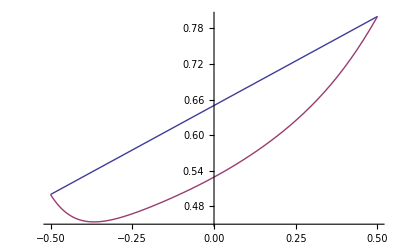

```mathematica
toplotBxlinear=FullSimplify[myBx[x]//.{dx->1,a2cleft->.5,a2cright->.8,F1->0,F2->0,F3->0,F4->0,F5->0,F6->0}]
toplotBxnonlinear=myBx[x]//.myF3F4//.{dx->1,a2cleft->.5,a2cright->.8,F1->.5,F2->0.7,F3->0.3,F4->0.9}
Plot[{toplotBxlinear,toplotBxnonlinear},{x,-1/2,1/2}]
```